# ECUACIONES DIFERENCIALES

## ECUACIONES DIFERENCIALES LINEALES DE SEGUNDO ORDEN CON COEFICIENTES CONSTANTES:

Fis. Jorge Chávez Carlos

Dada una ecuación de segundo orden con coeficientes constates de la forma :

a y''+b y'+c y=0

la función y(t) puede ser encontrada  definiendo los coeficientes:

```mathematica
a=1;
b=5;
c=6;
```

Una vez definidos los coeficientes basta ejecutar la siguiente instrucción :

## EJEMPLO:

```mathematica
DSolve[a y''[t]+b y'[t]+c y[t]==0,y[t],t]
```

{{y[t]→ⅇ^(-3 t) C[1]+ⅇ^(-2 t) C[2]}}

```mathematica
ω=2;
ωo=1.9;
```

```mathematica
DSolve[{y''[t]+ω^2 y[t]==Sin[ωo t],y[0]==0,y'[0]==1},y[t],t];
```

```mathematica
x[t_]=y[t]/.%
```

{2.5641 Cos[2. t]^2 Sin[1.9 t]-1.9359 Sin[2. t]+2.5641 Sin[1.9 t] Sin[2. t]^2}

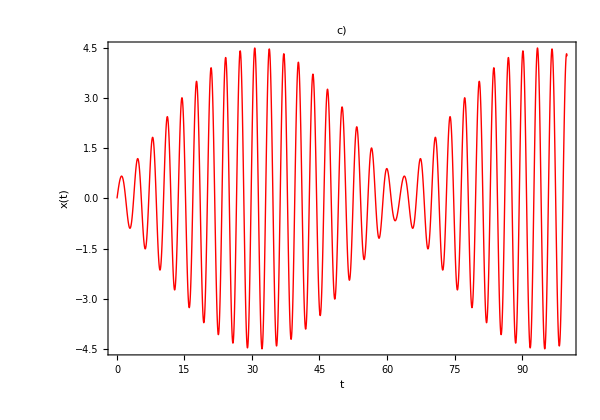

```mathematica
Plot[x[t],{t,0,100},FrameLabel->{"t","x(t)"},PlotLabel->"c)" ,Axes->False,Frame->True,ImageSize->600,PlotRange->All,AspectRatio->0.7,PlotStyle->{Thick,Red}]
```

```mathematica
GraphicsGrid[Map[{Plot[u[t],{t,0,100},FrameLabel->{"t","u(t)"},Axes->False,Frame->True,ImageSize->600,PlotRange->All,AspectRatio->0.7,PlotStyle->{Purple,Blue,Green,Yellow,Orange,Red}],Plot[u[t],{t,0,100},FrameLabel->{"t","u(t)"},Axes->False,Frame->True,ImageSize->600,PlotRange->All,AspectRatio->0.7,PlotStyle->{Purple,Blue,Green,Yellow,Orange,Red}]}]]
```

GraphicsGrid::list: … is not a list of lists.

GraphicsGrid[-Graphics-]